## Zadanie 1 - Część Praktyczna.

#### 1. Porównanie przebiegu funkcji π (x), Li (x) oraz x/(ln (x))

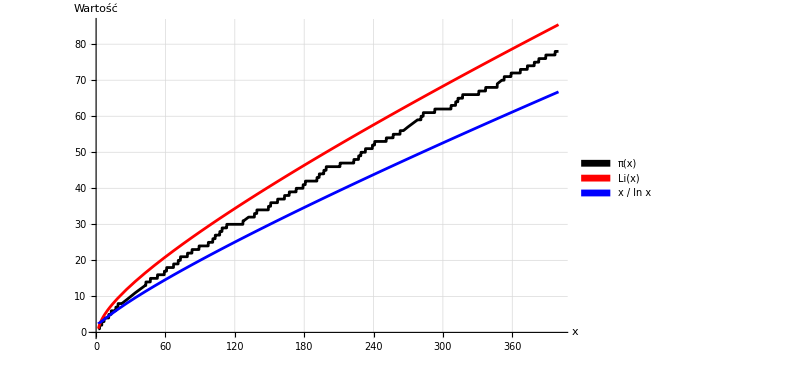

```mathematica
Plot[{PrimePi[x],LogIntegral[x],x/Log[x]},{x,2,400},PlotStyle->{Black,Red,Blue},PlotLegends->SwatchLegend[{Black,Red,Blue},{"π(x)","Li(x)","x / ln x"},LegendLabel->None],AxesLabel->{"x","Wartość"},GridLines->Automatic,ImageSize->600]
```

1. Li (x) lepiej przybliża π (x) niż x/ln (x)
2. Dla dużych x:Li(x)≈π(x), a x/ln(x) odbiega.

#### 2. Ilorazy: (π(x))/(Li(x))oraz (π(x))/(x/ln x)

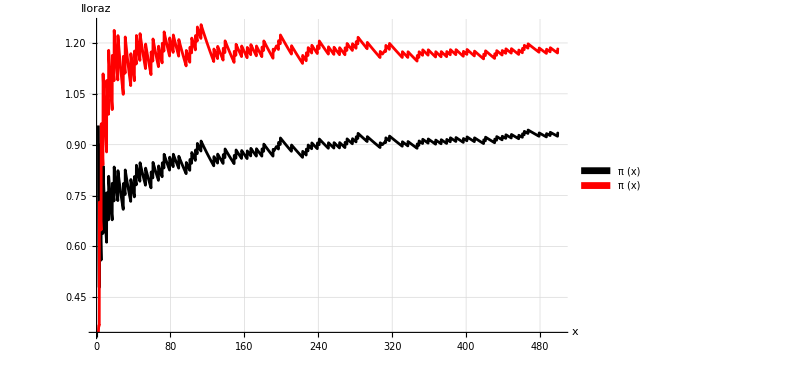

```mathematica
Plot[{PrimePi[x]/LogIntegral[x],PrimePi[x]/(x/Log[x])},{x,2,500},PlotStyle->{Black,Red},PlotLegends->SwatchLegend[{Black,Red},{"π (x)","π (x)"},LegendLabel->None],AxesLabel->{"x","Iloraz"},GridLines->Automatic,ImageSize->600]
```

1. π (x)/Li (x) → ~1 (zgodność z teorią)
2. π (x)/(x/ln (x)) → rośnie (słabsza zgodność)

#### 3. Różnice : π (x) - Li (x) oraz π (x) - (x/ln(x))

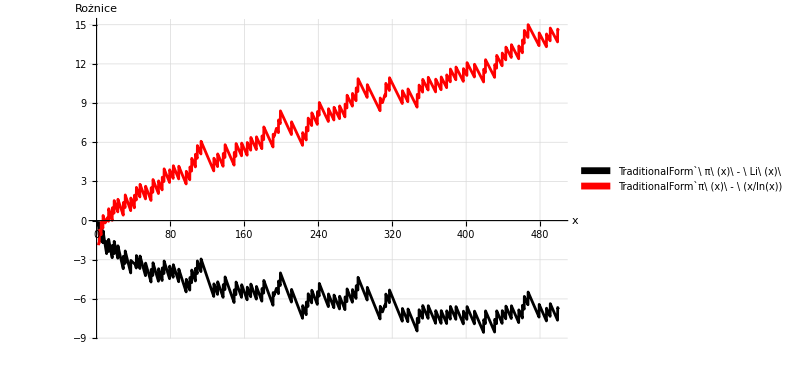

```mathematica
Plot[{PrimePi[x]-LogIntegral[x],PrimePi[x]-x/Log[x]},{x,2,500},PlotStyle->{Black,Red},PlotLegends->SwatchLegend[{Black,Red},{"TraditionalForm`\ π\ (x)\  - \ Li\ (x)\ ","TraditionalForm`π\ (x)\  - \ (x/ln(x))"},LegendLabel->None],AxesLabel->{"x","Rożnice"},GridLines->Automatic,ImageSize->600]
```

1. π(x)-Li(x)<0 (Li(x) przeszacowuje)
2. π(x)-x/ln(x)>0 (x/ln(x) niedoszacuje)

#### Podsumowanie:

Li(x) jest dokładniejszym oszacowaniem π(x). 
Porównanie tych przebiegów potwierdza twierdzenia o rozmieszczeniu liczb pierwszych.